```mathematica
maximalQ[mat1_]:=
Module[{t,mat2},
t=True;
Do[
If[i≠j&&mat1[[i,j]]==0,
mat2=mat1;
mat2[[i,j]]=1;
mat2[[j,i]]=1;
If[MemberQ[primegraphs,mat2],
t=False;
Break[]
]
],
{i,Length[mat1]},{j,i,Length[mat1]}
];
Return[t(*{t,AdjacencyGraph[mat2],MatrixForm[mat2-mat1]}*)];
];
primeGraphQ[mat1_]:=
Module[{t,mat2},
t=False;
mat2=MatrixPower[mat1,3];
If[ContainsOnly[Table[mat2[[k,k]],{k,Length[mat1]}],{0}],
If[ChromaticPolynomial[AdjacencyGraph[mat1],3]!=0,
t=True;
]];
Return[t];
];
```

```mathematica
findAllPrimeGraphs=
(Reap[
findPrimeGraphs[#1,1,1]
])&;
findPrimeGraphs[mat1_,starti_,startj_]:=
Module[{mat2,i,j},
i=starti;
j=startj;
If[i==Length[mat1]&&j>Length[mat1],
If[primeGraphQ[mat1],
Sow[mat1];],
If[j>Length[mat1],
i=i+1;
j=i;];
findPrimeGraphs[mat1,i,j+1];
If[i≠j,
mat2=mat1;
mat2[[i,j]]=1;
mat2[[j,i]]=1;
(*Echo[mat2];*)
findPrimeGraphs[mat2,i,j+1];];
]
];
findAllGraphs[mat1_,starti_,startj_]:=
Module[{mat2,i,j},
i=starti;
j=startj;
If[i==Length[mat1]&&j>Length[mat1],
If[True,
Sow[mat1];],
If[j>Length[mat1],
i=i+1;
j=i;];
findAllGraphs[mat1,i,j+1];
If[i≠j,
mat2=mat1;
mat2[[i,j]]=1;
mat2[[j,i]]=1;
(*Echo[mat2];*)
findAllGraphs[mat2,i,j+1];];
]
];
```

```mathematica
$RecursionLimit=10000
```

10000

```mathematica
AbsoluteTiming[graphs=Reap[findAllGraphs[ConstantArray[0,{7,7}],1,1]][[2,1]];]
AbsoluteTiming[Tuples[{0,1},{7,7}];]
```

{108.422,Null}

General::nomem: The current computation was aborted because there was insufficient memory available to complete the computation.

Throw::sysexc: Uncaught SystemException returned to top level. Can be caught with Catch[…, _SystemException].

SystemException[MemoryAllocationFailure]

```mathematica
Length[graphs]
```

2097152

```mathematica
AbsoluteTiming[primegraphs=Parallelize[Select[graphs,primeGraphQ]];]
Beep[]
(*SendMail["5127742864@txt.att.net","Prime Graphs Found"]*)
```

{301.282,Null}

```mathematica
AbsoluteTiming[maximalprimegraphs=Parallelize[Select[primegraphs,maximalQ]];]
Beep[]
(*SendMail[<|"To"->"5127742864@txt.att.net","Body"->{ToString[Evaluate[Length[maximalprimegraphs]]]," Maximal Prime Graphs Found"}|>]*)
```

{1380.56,Null}

```mathematica
DumpSave["7primegraphs.mx","Global`"]
```

{Global`}

```mathematica
Get["7primegraphs.mx"]
```

```mathematica
Length[maximalprimegraphs]
```

1743

```mathematica
maximalprimegraphs
```

{{{0,0,0,0,0,0,1},{0,0,0,0,0,0,1},{0,0,0,0,0,0,1},{0,0,0,0,0,0,1},{0,0,0,0,0,0,1},{0,0,0,0,0,0,1},{1,1,1,1,1,1,0}},{{0,0,0,0,0,1,0},{0,0,0,0,0,1,0},{0,0,0,0,0,1,0},{0,0,0,0,0,1,0},{0,0,0,0,0,1,0},{1,1,1,1,1,0,1},{0,0,0,0,0,1,0}},1739,{{0,1,1,1,1,1,0},{1,0,0,0,0,0,1},{1,0,0,0,0,0,1},{1,0,0,0,0,0,1},{1,0,0,0,0,0,1},{1,0,0,0,0,0,1},{0,1,1,1,1,1,0}},{{0,1,1,1,1,1,1},{1,0,0,0,0,0,0},{1,0,0,0,0,0,0},{1,0,0,0,0,0,0},{1,0,0,0,0,0,0},{1,0,0,0,0,0,0},{1,0,0,0,0,0,0}}}
 |  |  |  |

```mathematica
AbsoluteTiming[
isomaxprimegraphs=AdjacencyGraph/@maximalprimegraphs;
isomaxprimegraphs=Tuples[{isomaxprimegraphs,isomaxprimegraphs}];
isomaxprimegraphsbool=Reap[Do[Sow[IsomorphicGraphQ[isomaxprimegraphs[[i,1]],isomaxprimegraphs[[i,2]]]],{i,Length[isomaxprimegraphs]}]][[2,1]];
]
```

{21.7361,Null}

```mathematica
isomaxprimegraphs=AdjacencyGraph/@maximalprimegraphs;
```

```mathematica
Dimensions[isomaxprimegraphsbool]
```

{3038049}

```mathematica
isomaxgraphs=Reap[Do[
If[
Apply[BooleanCountingFunction[1,i],isomaxprimegraphsbool[[i;;((i-1)*Length[maximalprimegraphs]+i);;Length[maximalprimegraphs]]]],
Sow[maximalprimegraphs[[i]]]
],
{i,Length[maximalprimegraphs]}
]][[2,1]]
```

{{{0,0,0,0,0,0,1},{0,0,0,0,0,0,1},{0,0,0,0,0,0,1},{0,0,0,0,0,0,1},{0,0,0,0,0,0,1},{0,0,0,0,0,0,1},{1,1,1,1,1,1,0}},{{0,0,0,0,0,1,1},{0,0,0,0,0,1,1},{0,0,0,0,0,1,1},{0,0,0,0,0,1,1},{0,0,0,0,0,1,1},{1,1,1,1,1,0,0},{1,1,1,1,1,0,0}},{{0,0,0,0,0,1,1},{0,0,0,0,0,1,1},{0,0,0,0,0,1,1},{0,0,0,0,1,0,1},{0,0,0,1,0,1,0},{1,1,1,0,1,0,0},{1,1,1,1,0,0,0}},{{0,0,0,0,0,1,1},{0,0,0,0,0,1,1},{0,0,0,0,1,0,1},{0,0,0,0,1,0,1},{0,0,1,1,0,1,0},{1,1,0,0,1,0,0},{1,1,1,1,0,0,0}},{{0,0,0,0,0,1,1},{0,0,0,1,1,0,1},{0,0,0,1,1,0,1},{0,1,1,0,0,1,0},{0,1,1,0,0,1,0},{1,0,0,1,1,0,0},{1,1,1,0,0,0,0}},{{0,0,0,0,1,1,1},{0,0,0,0,1,1,1},{0,0,0,0,1,1,1},{0,0,0,0,1,1,1},{1,1,1,1,0,0,0},{1,1,1,1,0,0,0},{1,1,1,1,0,0,0}}}

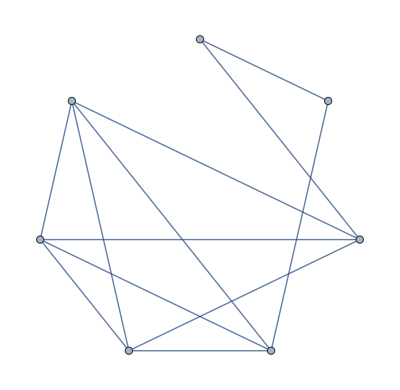
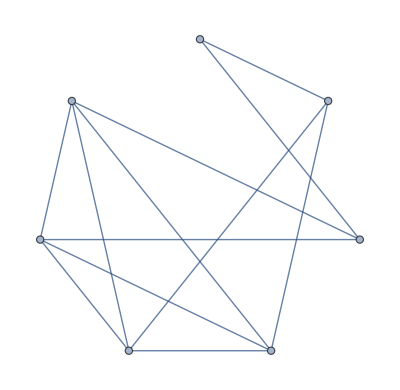
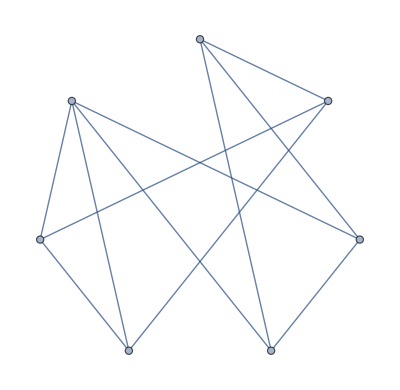

```mathematica
GraphComplement/@AdjacencyGraph/@Select[isomaxgraphs,ConnectedGraphQ[GraphComplement[AdjacencyGraph[#]]]&]
```

```mathematica
Head[ConnectedGraphQ[GraphComplement[AdjacencyGraph[#]]]&]
```

Function

```mathematica
isomaxprimegraphsbool[[3;;((3-1)*Length[maximalprimegraphs]+3);;Length[maximalprimegraphs]]]
```

{False,False,True}

```mathematica
IsomorphicGraphQ[isomaxprimegraphs[[1]],isomaxprimegraphs[[3]]]
```

False

```mathematica
Dimensions[isomaxgraphs]
```

{2}

```mathematica
AbsoluteTiming[isomaxgraphs=Tuples[{maximalprimegraphs,maximalprimegraphs}];]
Dimensions[isomaxgraphs]
```

{1.33162,Null}

{3038049,2,7,7}

{40000,2,7,7}

```mathematica
SendMail[<|"To"->"5127742864@txt.att.net","Body"->{ToString[Evaluate[Length[maximalprimegraphs]]],"Test"}|>]
```

Success[…]

```mathematica
maximalprimegraphs
```

maximalprimegraphs

```mathematica
Length[maximalprimegraphs]
```

15

```mathematica
maximalQ[testgraph]
```

{True,{{0,0,0,1,1,1,1},{0,0,1,1,1,1,0},{0,1,0,0,0,0,1},{1,1,0,0,0,0,0},{1,1,0,0,0,0,0},{1,1,0,0,0,0,1},{1,0,1,0,0,1,0}}}

```mathematica
Position[primegraphs,testgraph]
```

{{58233}}

```mathematica
graph1={{0,1,0,0,1,1,0,0,1,0,0},{1,0,1,0,0,0,0,1,0,0,1},{0,1,0,1,0,0,1,0,0,1,0},{0,0,1,0,1,1,0,0,1,0,0},{1,0,0,1,0,0,0,1,0,0,1},{1,0,0,1,0,0,1,0,0,0,1},{0,0,1,0,0,1,0,1,0,0,0},{0,1,0,0,1,0,1,0,1,0,0},{1,0,0,1,0,0,0,1,0,1,0},{0,0,1,0,0,0,0,0,1,0,1},{0,1,0,0,1,1,0,0,0,1,0}};
graph2={{0,1,0,0,1,0,0,0,0,0,1},{1,0,1,0,0,0,1,0,0,1,0},{0,1,0,1,0,1,0,0,1,0,0},{0,0,1,0,1,0,0,1,0,0,1},{1,0,0,1,0,0,1,0,0,1,0},{0,0,1,0,0,0,1,0,0,0,1},{0,1,0,0,1,1,0,1,0,0,0},{0,0,0,1,0,0,1,0,1,0,0},{0,0,1,0,0,0,0,1,0,1,0},{0,1,0,0,1,0,0,0,1,0,1},{1,0,0,1,0,1,0,0,0,1,0}};
graph3={{0,1,0,0,1,0,0,0,0,0,0},{1,0,1,0,0,0,0,0,0,0,0},{0,1,0,1,0,0,0,0,0,0,0},{0,0,1,0,1,0,0,0,0,0,0},{1,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,1},{0,0,0,0,0,1,0,1,0,0,0},{0,0,0,0,0,0,1,0,1,0,0},{0,0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,1,0,1},{0,0,0,0,0,1,0,0,0,1,0}};
```